```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/peeter/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

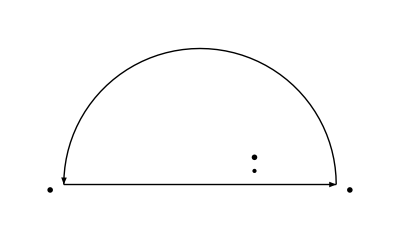

```mathematica
ClearAll[R, lineArrow, xrange1, r, semicircleArrow, greensHelmholtzFig1, epsilon, k]
R=5; 
k = 2;
epsilon = 0.5;
xrange1 = {{-R,0},{R, 0}};

lineArrow[s_, t_]:=Graphics[{
Thick,Arrow[xrange1],
Text[MaTeX["-R"], {-1.1 R, -0.2}],
Text[MaTeX["R"], {1.1 R, -0.2}],
Text[MaTeX[t], {s k, 2 s epsilon}],
PointSize -> Large,

Point[{s k,s epsilon}]
}];

semicircleArrow[a_, s_]:=Graphics[{Thick,Arrow[Table[{a Cos[t],a Sin[t]},{t,s,s + Pi,Pi/50}]]}]

greensHelmholtzFig1 = Show[lineArrow[1, "k + i \\epsilon"],semicircleArrow[R, 0],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-1,R+1}},Axes->False,Ticks->None,Frame->False]
```

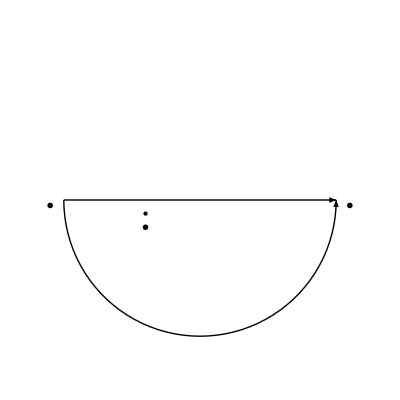

```mathematica
ClearAll[greensHelmholtzFig2]

greensHelmholtzFig2 = Show[lineArrow[-1, "-k - i \\epsilon"],semicircleArrow[R, Pi],AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-R-1,R+1}},Axes->False,Ticks->None,Frame->False]
```

```mathematica
peeters`exportForLatex["greensHelmholtzFig1",greensHelmholtzFig1]
peeters`exportForLatex["greensHelmholtzFig2",greensHelmholtzFig2]
```

{greensHelmholtzFig1.eps,greensHelmholtzFig1pn.png}

{greensHelmholtzFig2.eps,greensHelmholtzFig2pn.png}